```mathematica
path = FileNameJoin[Drop[#,Flatten@{Position[#,"Master"]+1,-1}]&@StringSplit[NotebookDirectory[],"\\"]];
```

```mathematica
ClearAll[data11]
data11=Table[Import[path<>"\\Data\\2017\\may\\11\\may11_"<>ToString[i]<>".dat"],{i,6,9}];
```

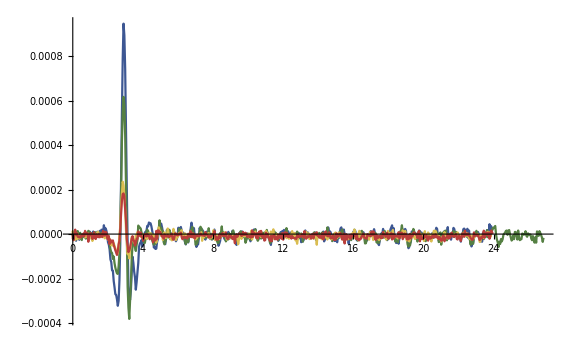

```mathematica
ListLinePlot[Table[data11[[i,All,{3,2}]],{i,1,4}],PlotRange->All,ImageSize->Large,PlotStyle->"DarkRainbow"]
```